```mathematica
A={{100,100,100,100},{83,93,97,57},{82,60,99,79},{93,96,85,89},{98,91,99,68}};
b={100,80,82,90,86};
soln5=Solve[A[[{1,2,3,4}]].{x1,x2,x3,x4}==b[[{1,2,3,4}]],{x1,x2,x3,x4}]//N
soln4=Solve[A[[{1,2,3,5}]].{x1,x2,x3,x4}==b[[{1,2,3,5}]],{x1,x2,x3,x4}]//N
soln3=Solve[A[[{1,2,4,5}]].{x1,x2,x3,x4}==b[[{1,2,4,5}]],{x1,x2,x3,x4}]//N
soln2=Solve[A[[{1,3,4,5}]].{x1,x2,x3,x4}==b[[{1,3,4,5}]],{x1,x2,x3,x4}]//N
soln1=Solve[A[[{2,3,4,5}]].{x1,x2,x3,x4}==b[[{2,3,4,5}]],{x1,x2,x3,x4}]//N
```

{{x1→0.231548,x2→0.167149,x3→0.274059,x4→0.327243}}

{{x1→0.116399,x2→0.198271,x3→0.320897,x4→0.364433}}

{{x1→0.13181,x2→0.22925,x3→0.282998,x4→0.355941}}

{{x1→0.257259,x2→0.13019,x3→0.235092,x4→0.377459}}

{{x1→0.110022,x2→0.205669,x3→0.312458,x4→0.376009}}

```mathematica
sol={soln1,soln2,soln3,soln4,soln5}
```

```mathematica
sol={{{0.1100218100532011,0.20566921088059187,0.31245838640680107,0.37600859074086956}},{{0.25725881985638466,0.1301904464564471,0.23509210115516704,0.37745863253200124}},{{0.13180987202925046,0.22925045703839123,0.2829981718464351,0.3559414990859232}},{{0.11639859717015359,0.198270649413472,0.3208973273672754,0.36443342604909906}},{{0.23154848046309695,0.16714905933429810,0.2740593342981187,0.32724312590448623}}}
```

{{{0.110022,0.205669,0.312458,0.376009}},{{0.257259,0.13019,0.235092,0.377459}},{{0.13181,0.22925,0.282998,0.355941}},{{0.116399,0.198271,0.320897,0.364433}},{{0.231548,0.167149,0.274059,0.327243}}}

```mathematica
Total[sol]/5
```

{{0.169408,0.186106,0.285101,0.360217}}

```mathematica
17+19+28+36
```

100

```mathematica
A.{17,19,28,36}
```

{10000,7946,8150,8989,8615}

```mathematica
b
```

{100,80,82,90,86}

```mathematica
N[soln]
```

{{x1→0.231548,x2→0.167149,x3→0.274059,x4→0.327243}}

```mathematica
c={8,3,6,2,421,2};
```

```mathematica
c[[{1,3,4}]]
```

{8,6,2}

```mathematica
Solve [{Aᵀ.A.{x1,x2,x3,x4}==Aᵀ.b},{x1,x2,x3,x4}]//N
```

{{x1→0.121987,x2→0.200536,x3→0.31161,x4→0.367779}}

```mathematica
Solve[Aᵀ.A.{x1,x2,x3,x4}==
```

```mathematica
A.{0.12,0.2,0.31,0.37}
```

{100.,79.72,81.76,89.64,85.81}

```mathematica
AA=({{100, 100, 100}, {94, 86, 97}, {71, 57, 71}, {96, 94, 98}, {74, 66, 100}, {98, 33, 77}, {75, 26, 63}, {100, 100, 86}});
cutoffs={100,93,88,83,76,71,66,61,56,50,0};
grades=Table[(cutoffs[[i+1]]+cutoffs[[i]])/2,{i,1,10}]//N;
thegrades={1,1,6,1,3,7,9,2};
bb=grades[[thegrades]];
```

```mathematica
Solve[{AAᵀ.AA.{x1,x2,x3}==AAᵀ.bb},{x1,x2,x3}]
```

{{x1→0.0812364,x2→0.307572,x3→0.606197}}

```mathematica
AA.{0.08,0.31,0.61}
```

{100.,93.35,66.66,96.6,87.38,65.04,52.49,91.46}

```mathematica
AA.{0.1,0.3,0.6}
```

{100.,93.4,66.8,96.6,87.2,66.,89.1,93.4}

```mathematica
Map[{#,Sin[#]}&,Range[0,π/2,0.25]]//MatrixForm
```

(0. | 0.
0.25 | 0.247404
0.5 | 0.479426
0.75 | 0.681639
1. | 0.841471
1.25 | 0.948985
1.5 | 0.997495)

```mathematica
π/2//N
```

1.5708

```mathematica
xx = {0.,0.25,0.5,0.75,1.,1.25,1.5}
yy = {0.,0.2474,.47943,.68164,.84147,.94898,.9975}
```

{0.,0.25,0.5,0.75,1.,1.25,1.5}

{0.,0.2474,0.47943,0.68164,0.84147,0.94898,0.9975}

```mathematica
b=.
```

```mathematica
b=(Total[xx^2]Total[yy]-Total[xx]Total[xx yy])/(7Total[xx^2]-Total[xx]^2)
```

0.089735

```mathematica
m=(7Total[xx yy]-Total[xx]Total[yy])/(7Total[xx^2]-Total[xx]^2)
```

0.679671

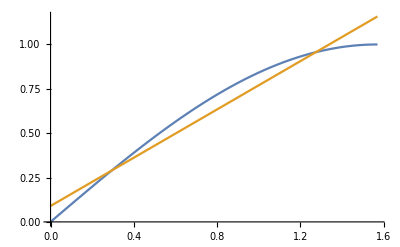

```mathematica
Plot[{Sin[x],0.0897+0.680 x},{x,0,π/2}]
```

```mathematica
p3[x_]:={1,x,x^2,x^3}
```

```mathematica
A=. ;b=.
```

```mathematica
A=Map[p3,xx]; MatrixForm[A]
```

(1 | 0. | 0. | 0.
1 | 0.25 | 0.0625 | 0.015625
1 | 0.5 | 0.25 | 0.125
1 | 0.75 | 0.5625 | 0.421875
1 | 1. | 1. | 1.
1 | 1.25 | 1.5625 | 1.95313
1 | 1.5 | 2.25 | 3.375)

```mathematica
soln=SolveValues[Aᵀ.A.{c0,c1,c2,c3}==Aᵀ.yy,{c0,c1,c2,c3}][[1]]
```

{-0.000540238,1.01896,-0.0596648,-0.117547}

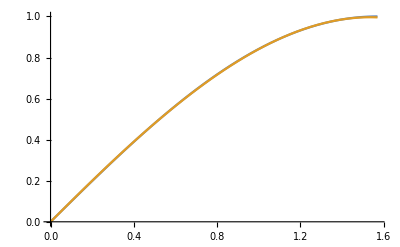

```mathematica
Plot[{Sin[x],-.0005+1.019x-.0597x^2-.118x^3},{x,0,π/2}]
```

```mathematica
{-0.0005402380952365059,1.0189552380952231,-0.059664761904738725,-0.11754666666667594}.p3[1.1]
```

0.891662

```mathematica
Sin[1.1]//N
```

0.891207

```mathematica
p7[x_]:={1,x,x^2,x^3,x^4,x^5,x^6,x^7}
```

```mathematica
A=Map[p7,xx]; MatrixForm[A]
```

(1 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
1 | 0.25 | 0.0625 | 0.015625 | 0.00390625 | 0.000976563 | 0.000244141 | 0.0000610352
1 | 0.5 | 0.25 | 0.125 | 0.0625 | 0.03125 | 0.015625 | 0.0078125
1 | 0.75 | 0.5625 | 0.421875 | 0.316406 | 0.237305 | 0.177979 | 0.133484
1 | 1. | 1. | 1. | 1. | 1. | 1. | 1.
1 | 1.25 | 1.5625 | 1.95313 | 2.44141 | 3.05176 | 3.8147 | 4.76837
1 | 1.5 | 2.25 | 3.375 | 5.0625 | 7.59375 | 11.3906 | 17.0859)

```mathematica
soln=Solve[Aᵀ.A.{c0,c1,c2,c3,c4,c5,c6,c7}==Aᵀ.yy,{c0,c1,c2,c3,c4,c5,c6,c7}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c0→-1.45313×10^-12,c2→9.79939-9.8 c1,c3→-36.2516+36.0889 c1,c4→65.3238-65.3333 c1,c5→-62.2031+62.2222 c1,c6→29.8609-29.8667 c1,c7→-5.68787+5.68889 c1}}

```mathematica
soln=SolveValues[Aᵀ.A.{0,1,c2,c3,c4,c5,c6,c7}==Aᵀ.yy,{c2,c3,c4,c5,c6,c7}][[1]]
```

{-0.000611244,-0.162675,-0.00954756,0.0190945,-0.0058112,0.00102021}

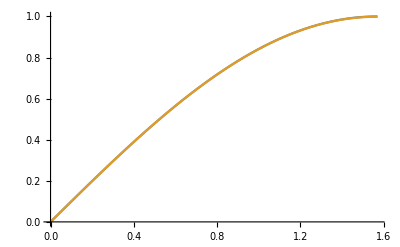

```mathematica
Plot[{Sin[x],0+1.x-.000611x^2-.163x^3-.00955x^4+.0191x^5-.00581x^6+.00102x^7},{x,0,π/2}]
```

```mathematica
{0,1,-0.000611244483113531,-0.16267472562413607,-0.00954755638487754,0.019094519555731566,-0.005811200602907013,0.0010202075395670729}.p7[1.1]
```

0.891207

```mathematica
Sin[1.1]//N
```

0.891207

```mathematica
po[x_]:={x,x^3,x^5,x^7,x^9}
```

```mathematica
A=Map[po,xx];A//MatrixForm
```

(0. | 0. | 0. | 0. | 0.
0.25 | 0.015625 | 0.000976563 | 0.0000610352 | 3.8147×10^-6
0.5 | 0.125 | 0.03125 | 0.0078125 | 0.00195313
0.75 | 0.421875 | 0.237305 | 0.133484 | 0.0750847
1. | 1. | 1. | 1. | 1.
1.25 | 1.95313 | 3.05176 | 4.76837 | 7.45058
1.5 | 3.375 | 7.59375 | 17.0859 | 38.4434)

```mathematica
soln=SolveValues[Aᵀ.A.{c1,c3,c5,c7,c9}==Aᵀ.yy,{c1,c3,c5,c7,c9}][[1]]
```

{0.99999,-0.166586,0.00819564,-0.000118055,-0.000012384}

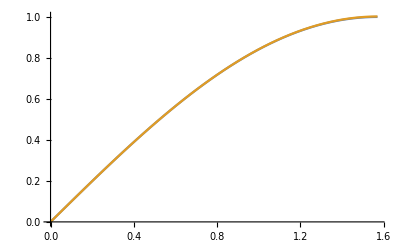

```mathematica
Plot[{Sin[x],1.x-.166x^3+.00820x^5-.000118x^7-.0000124x^9},{x,0,π/2}]
```

```mathematica
{0.9999897781327217,-0.1665858236976505,0.008195638896643846,-0.00011805513496775891,-0.000012383976408018666}.po[1.1]
```

0.891203

```mathematica
ap=1.x-.166x^3+.00820x^5-.000118x^7-.0000124x^9/.x->1.1
```

0.892001

```mathematica
tv=Sin[1.1]//N
```

0.891207

```mathematica
ap-tv
```

0.000793635

```mathematica
{1,2,3,10,11,12,19,20,21}+3(i-1)+3 9 (j-1)
```

```mathematica
1!=x
```

1≠x

```mathematica
SameQ[1,x]
```

False

```mathematica
!True
```

False